```mathematica
Clear[hbar, e0, m0, ηm];
hbar=6.58211899*10^(-16);  (* h/2π  in eV s *)
m0=9.10938215*10^(-31); 
e0=1.602176487*10^(-19);
ηm=hbar^2*e0*10^(20)/m0;  (* hbar^2/m0 in eV A^2 *)
μB=5.7883818066 * 10^(-2);    (* in meV/T *)
meVpK=8.6173325*10^(-2);   (* Kelvin into meV *)
(* **************************************** *)
```

```mathematica
Clear[ts, tsw, as, ms, Nx, Ny, Nxn, α, αw, Δ];
as=100.0; (* unit cell in A *)
ms=0.02;
ts=500*ηm/(2*as^2*ms); (* hopping in meV *)
α=200.0/as; (* Rashba coupling in meV *)
Δ=0.4; (* induced gap in meV *)
Nx=250;
NxM=10;
Nxn=0;
Ny=1;
asw=600.0/(Ny+1);
αw=α*as/asw;
tsw=4.0;
μ=0.0;
B=2Δ;

(*tϕ=ts/200;
αϕ=α/200;*)
tϕ1=0.4ts;
tϕ2=ts;
αϕ=0.0;
θ1=-0.5π;
θM=0.5 π;
θ2=0.5 π;
```

```mathematica
a=SessionTime[];
Iθ={};
Imax={};
For[θM=0.0,θM≤2π,θM+=0.01 π,
eϕ={};
elϕ=Table[{},{n,1,10}];
For[ϕ=0,ϕ≤4π,ϕ+=0.1,

ϵ0=2ts Cos[Pi/(Nx+1.0)];
(*First Chain*)
H1σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ1],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ1],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ12τ11=SparseArray[{Band[{1,1}]->B Cos[θ1],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H1σ21τ11=SparseArray[{Band[{1,1}]->B Cos[θ1],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H1σ12τ12=SparseArray[{Band[{1,1}]->Δ},{Nx,Nx}];
H1σ21τ12=SparseArray[{Band[{1,1}]->-Δ},{Nx,Nx}];

H1τ11=SparseArray[ArrayFlatten[{{H1σ11τ11,H1σ12τ11},{H1σ21τ11,H1σ22τ11}}]];
H1τ22=-H1τ11;
H1τ12=SparseArray[ArrayFlatten[{{0,H1σ12τ12},{H1σ21τ12,0}}]];
H1τ21=Conjugate[Transpose[H1τ12]];

H11=SparseArray[ArrayFlatten[{{H1τ11,H1τ12},{H1τ21,H1τ22}}]];


(*Middle Chain*)
HMσ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θM],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θM],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ12τ11=SparseArray[{Band[{1,1}]->B Cos[θM],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{NxM,NxM}];
HMσ21τ11=SparseArray[{Band[{1,1}]->B Cos[θM],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{NxM,NxM}];

HMσ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];
HMσ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];

HMτ11=SparseArray[ArrayFlatten[{{HMσ11τ11,HMσ12τ11},{HMσ21τ11,HMσ22τ11}}]];
HMτ22=-HMτ11;
HMτ12=SparseArray[ArrayFlatten[{{0,HMσ12τ12},{HMσ21τ12,0}}]];
HMτ21=Conjugate[Transpose[HMτ12]];

HMM=SparseArray[ArrayFlatten[{{HMτ11,HMτ12},{HMτ21,HMτ22}}]];


(*Second Chain*)
H2σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ2],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ2],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ12τ11=SparseArray[{Band[{1,1}]->B Cos[θ2],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H2σ21τ11=SparseArray[{Band[{1,1}]->B Cos[θ2],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H2σ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];
H2σ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];

H2τ11=SparseArray[ArrayFlatten[{{H2σ11τ11,H2σ12τ11},{H2σ21τ11,H2σ22τ11}}]];
H2τ22=-H2τ11;
H2τ12=SparseArray[ArrayFlatten[{{0,H2σ12τ12},{H2σ21τ12,0}}]];
H2τ21=Conjugate[Transpose[H2τ12]];

H22=SparseArray[ArrayFlatten[{{H2τ11,H2τ12},{H2τ21,H2τ22}}]];

(*Tunnel Junction*)
H1M=SparseArray[{{Nx,1}->tϕ1,{2Nx,NxM+1}->tϕ1,{3Nx,2NxM+1}->-tϕ1,{4Nx,3NxM+1}->-tϕ1},{4Nx,4NxM}];
HM1=Conjugate[Transpose[H1M]];

HM2=SparseArray[{{NxM,1}->tϕ2,{2NxM,Nx+1}->tϕ2,{3NxM,2Nx+1}->-tϕ2,{4NxM,3Nx+1}->-tϕ2},{4NxM,4Nx}];
H2M=Conjugate[Transpose[HM2]];

(*Full Wire*)
Hsp=SparseArray[ArrayFlatten[{{H11,H1M,0},{HM1,HMM,HM2},{0,H2M,H22}}]];



etp=Sort[Eigenvalues[Hsp,-10]];
For[n=1,n≤Length[etp],n++,
elϕ[[n]]=Join[elϕ[[n]],{{ϕ,etp[[n]]}}]
];
If[π<ϕ<3π,
eϕ=Join[eϕ,{{ϕ,Sum[etp[[i]],{i,1,Length[etp]/2-2}]+etp[[Length[etp]/2+1]]+etp[[Length[etp]/2+2]]}}];
,
eϕ=Join[eϕ,{{ϕ,Sum[etp[[i]],{i,1,Length[etp]/2-2}]+etp[[Length[etp]/2-1]]+etp[[Length[etp]/2]]}}];
];


];

Iϕ={};
IϕM={};
For[ϕi=2,ϕi≤Length[eϕ],ϕi++,
Iϕ=Join[Iϕ,{{eϕ[[ϕi,1]],(eϕ[[ϕi,2]]-eϕ[[ϕi-1,2]])/(eϕ[[ϕi,1]]-eϕ[[ϕi-1,1]])}}];
IϕM=Join[IϕM,{Re[(eϕ[[ϕi,2]]-eϕ[[ϕi-1,2]])/(eϕ[[ϕi,1]]-eϕ[[ϕi-1,1]])]}];
];

Iθ=Join[Iθ,{Iϕ}];
Imax=Join[Imax,{{θM,Max[IϕM]}}];
Print[{θM,Max[IϕM]}];
];
```

{0.,0.0180998}

{0.0314159,0.0178641}

{0.0628319,0.0176208}

{0.0942478,0.0173699}

{0.125664,0.0171114}

{0.15708,0.0168455}

{0.188496,0.0165725}

{0.219911,0.0162922}

{0.251327,0.016005}

{0.282743,0.0157109}

{0.314159,0.01541}

{0.345575,0.0151026}

{0.376991,0.0147888}

{0.408407,0.0144687}

{0.439823,0.0141426}

{0.471239,0.0138105}

{0.502655,0.0134727}

{0.534071,0.0131293}

{0.565487,0.0127806}

{0.596903,0.0124267}

{0.628319,0.0120678}

{0.659734,0.0117041}

{0.69115,0.0113358}

{0.722566,0.0109633}

{0.753982,0.0105865}

{0.785398,0.0102058}

{0.816814,0.00982141}

{0.84823,0.00943352}

{0.879646,0.00904242}

{0.911062,0.00864829}

{0.942478,0.00825132}

{0.973894,0.00785183}

{1.00531,0.00744996}

{1.03673,0.00704609}

{1.06814,0.00664028}

{1.09956,0.00623287}

{1.13097,0.00582409}

{1.16239,0.00541409}

{1.19381,0.00500316}

{1.22522,0.00459152}

{1.25664,0.00417941}

{1.28805,0.00376701}

{1.31947,0.00335457}

{1.35088,0.00294231}

{1.3823,0.00253039}

{1.41372,0.00211911}

{1.44513,0.00170863}

{1.47655,0.00129977}

{1.50796,0.000892108}

{1.53938,0.000486778}

{1.5708,0.0000939419}

{1.60221,0.000331588}

{1.63363,0.000730487}

{1.66504,0.00112947}

{1.69646,0.00152658}

{1.72788,0.00192128}

{1.75929,0.00231346}

{1.79071,0.00270297}

{1.82212,0.00309006}

{1.85354,0.0034741}

{1.88496,0.00385508}

{1.91637,0.00423282}

{1.94779,0.00460717}

{1.9792,0.00497802}

{2.01062,0.00534529}

{2.04204,0.00570885}

{2.07345,0.00606857}

{2.10487,0.00642427}

{2.13628,0.00677596}

{2.1677,0.00712352}

{2.19911,0.00746687}

{2.23053,0.00780573}

{2.26195,0.00814032}

{2.29336,0.00847017}

{2.32478,0.00879545}

{2.35619,0.00911598}

{2.38761,0.00943165}

{2.41903,0.00974236}

{2.45044,0.010048}

{2.48186,0.0103491}

{2.51327,0.0106459}

{2.54469,0.0109379}

{2.57611,0.0112252}

{2.60752,0.0115077}

{2.63894,0.0117859}

{2.67035,0.0120598}

{2.70177,0.0123316}

{2.73319,0.0126081}

{2.7646,0.0128829}

{2.79602,0.0131616}

{2.82743,0.013441}

{2.85885,0.0137108}

{2.89027,0.0139781}

{2.92168,0.0142304}

{2.9531,0.0144674}

{2.98451,0.0146898}

{3.01593,0.0148986}

{3.04734,0.0150941}

{3.07876,0.0152788}

{3.11018,0.015451}

{3.14159,0.0156102}

{3.17301,0.0157565}

{3.20442,0.0158895}

{3.23584,0.0160085}

{3.26726,0.0161129}

{3.29867,0.0162019}

{3.33009,0.0162745}

{3.3615,0.0163294}

{3.39292,0.0163654}

{3.42434,0.0163809}

{3.45575,0.0163741}

{3.48717,0.0163429}

{3.51858,0.0162853}

{3.55,0.0161986}

{3.58142,0.0160801}

{3.61283,0.0159268}

{3.64425,0.0157357}

{3.67566,0.0155059}

{3.70708,0.0152312}

{3.7385,0.0149074}

{3.76991,0.0145301}

{3.80133,0.0140949}

{3.83274,0.0136004}

{3.86416,0.0130473}

{3.89557,0.0124246}

{3.92699,0.0117405}

{3.95841,0.0109861}

{3.98982,0.0101729}

{4.02124,0.00929945}

{4.05265,0.00837242}

{4.08407,0.00740201}

{4.11549,0.00640282}

{4.1469,0.0053861}

{4.17832,0.00437178}

{4.20973,0.00338074}

{4.24115,0.00243652}

{4.27257,0.00156846}

{4.30398,0.00258459}

{4.3354,0.00367521}

{4.36681,0.00478798}

{4.39823,0.00590186}

{4.42965,0.00699801}

{4.46106,0.0080667}

{4.49248,0.0090992}

{4.52389,0.0100875}

{4.55531,0.0110245}

{4.58673,0.0119183}

{4.61814,0.012752}

{4.64956,0.0135395}

{4.68097,0.0142681}

{4.71239,0.0149479}

{4.7438,0.015579}

{4.77522,0.0161595}

{4.80664,0.0166923}

{4.83805,0.0171826}

{4.86947,0.0176361}

{4.90088,0.0180503}

{4.9323,0.0184282}

{4.96372,3.93403}

{4.99513,3.87964}

{5.02655,3.96543}

{5.05796,3.98944}

{5.08938,4.01838}

{5.1208,2.5319}

{5.15221,4.07109}

{5.18363,4.0645}

{5.21504,3.99626}

{5.24646,4.22625}

{5.27788,0.740976}

{5.30929,4.32689}

{5.34071,0.0876174}

{5.37212,2.5247}

{5.40354,2.48833}

{5.43496,0.541498}

{5.46637,4.70085}

{5.49779,0.045728}

{5.5292,0.0233691}

{5.56062,0.0266236}

{5.59203,0.0213606}

{5.62345,2.51474}

{5.65487,0.0210265}

{5.68628,0.0209687}

{5.7177,0.0209006}

{5.74911,0.0208226}

{5.78053,0.0207346}

{5.81195,0.0206369}

{5.84336,0.0205298}

{5.87478,0.0204132}

{5.90619,0.0202874}

{5.93761,0.0201525}

{5.96903,0.0200087}

{6.00044,0.0198559}

{6.03186,0.0196944}

{6.06327,0.0195243}

{6.09469,0.0193456}

{6.12611,0.0191584}

{6.15752,0.018963}

{6.18894,0.0187593}

{6.22035,0.0185475}

{6.25177,0.0183276}

{6.28319,0.0180998}

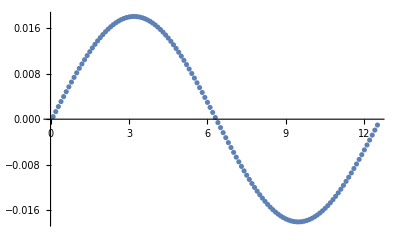

```mathematica
ListPlot[Re[Iθ[[1]]],PlotRange->All]
```

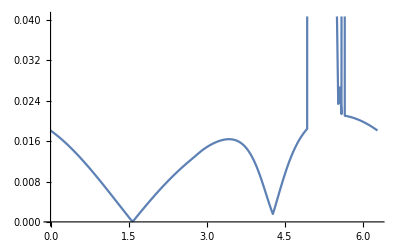

```mathematica
ListPlot[Imax,Joined->True]
```

```mathematica
(*Export["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Sparse Matrix\\Data\\Imax.mx",Imax]
Export["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Sparse Matrix\\Data\\Iθ.mx",Iθ]*)
```

```mathematica
(*Export["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Sparse Matrix\\Data\\Imax_θ1_π_θ2_05π.mx",Imax]
Export["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Sparse Matrix\\Data\\Iθ_θ1_π_θ2_05π.mx",Iθ]*)
(*Export["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Sparse Matrix\\Data\\Imax_θ1_05π_θ2_m05π.mx",Imax]
Export["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Sparse Matrix\\Data\\Iθ_θ1_05π_θ2_m05π.mx",Iθ]*)
```

```mathematica
ImaxI=Import["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Sparse Matrix\\Data\\Imax.mx"];
IθI=Import["C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\Sparse Matrix\\Data\\Iθ.mx"];
```

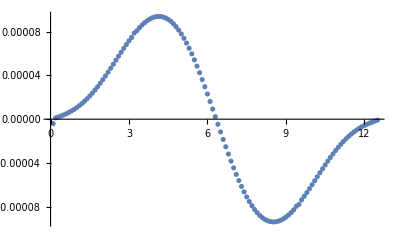

```mathematica
ListPlot[Re[IθI[[1]]],PlotRange->All]
```

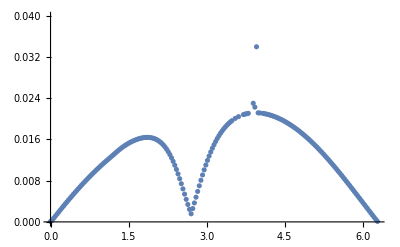

```mathematica
ListPlot[ImaxI]
```